## 1. Baseline outputs for n^* and g_{10}^*

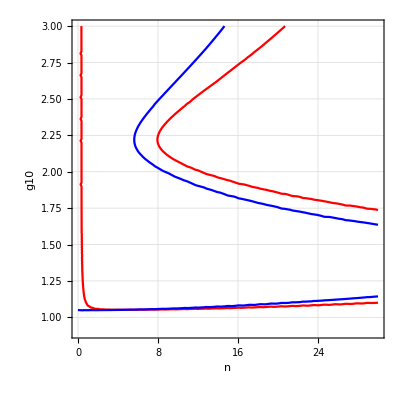

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,dparital,CriticalCondition];

phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

h=0.008;beta=Pi/8;lamdaf=0.96;phif=0.6;KK=0.175;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;

ContourPlot[{CriticalCondition==0,dparital==0},{n,0,30},{g10,0.9,3},ContourStyle->{Red,Blue},FrameLabel->{"n","g10"},GridLines->Automatic]
```

```mathematica
solution=FindRoot[{CriticalCondition==0,dparital==0},{{n,5},{g10,1.01}}]
g10older=g10/. solution
nolder=n/. solution
```

{n→4.7307,g10→1.05152}

1.05152

4.7307

```mathematica
g10older=1.0515238928342359;
nolder=4.730699457732493;

betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;
```

## 2. Older_decrease n^* by 10% and increase g_{10}^* by 10%

### 2.1 w=0

#### 2.1.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];
g10older=1.0515238928342359;
nolder=4.730699457732493;

betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10older*1.1;
n=nolder*0.9;

w=0;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v1h1=h/.  bestSol
v1KK1=KK/. bestSol
v1beta1=beta/. bestSol
v1lamdaf1=lamdaf/. bestSol
v1phif1=phif/. bestSol
```

0.015

0.100001

0.974133

0.956552

0.550033

#### 2.1.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10older*1.1;
ns=nolder*0.9;


lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.15;
ninit=4.4;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse1g101=g10/. sol;
inverse1n1=n/. sol;

err1g101=(inverse1g101-g10s)/g10s
err1n1=(inverse1n1-ns)/ns
```

-3.53221×10^-13

2.71114×10^-10

### 2.2 w=0.5

#### 2.2.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];

g10older=1.0515238928342359;
nolder=4.730699457732493;

betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10older*1.1;
n=nolder*0.9;

w=0.5;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v1h2=h/.  bestSol
v1KK2=KK/. bestSol
v1beta2=beta/. bestSol
v1lamdaf2=lamdaf/. bestSol
v1phif2=phif/. bestSol
```

0.00896431

0.166716

0.383741

0.885857

0.668251

#### 2.2.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10older*1.1;
ns=nolder*0.9;


lamdaf=v1lamdaf2;
beta=v1beta2;
h=v1h2;
KK=v1KK2;
phif=v1phif2;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.1576;
ninit=4.8699;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse1g102=g10/. sol;
inverse1n2=n/. sol;

err1g102=(inverse1g102-g10s)/g10s
err1n2=(inverse1n2-ns)/ns
```

4.30721×10^-7

0.000366554

### 2.3 w=1

#### 2.3.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];

g10older=1.0515238928342359;
nolder=4.730699457732493;

betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10older*1.1;
n=nolder*0.9;

w=1;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v1h3=h/.  bestSol
v1KK3=KK/. bestSol
v1beta3=beta/. bestSol
v1lamdaf3=lamdaf/. bestSol
v1phif3=phif/. bestSol
```

0.00913432

0.169574

0.387792

0.8862

0.644583

#### 2.3.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10older*1.1;
ns=nolder*0.9;


lamdaf=v1lamdaf3;
beta=v1beta3;
h=v1h3;
KK=v1KK3;
phif=v1phif3;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.1576;
ninit=4.8699;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse1g103=g10/. sol;
inverse1n3=n/. sol;

err1g103=(inverse1g103-g10s)/g10s
err1n3=(inverse1n3-ns)/ns
```

1.04845×10^-6

0.00087553

## 3. Older_decrease n^* by 20% and increase g_{10}^* by 20%

### 3.1 w=0

#### 3.1.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];


g10older=1.0515238928342359;
nolder=4.730699457732493;

betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10older*1.2;
n=nolder*0.8;

w=0;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v2h1=h/.  bestSol
v2KK1=KK/. bestSol
v2beta1=beta/. bestSol
v2lamdaf1=lamdaf/. bestSol
v2phif1=phif/. bestSol
```

0.0149909

0.100077

0.905425

0.924288

0.706634

#### 3.1.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10older*1.2;
ns=nolder*0.8;


lamdaf=v2lamdaf1;
beta=v2beta1;
h=v2h1;
KK=v2KK1;
phif=v2phif1;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.26285210108347;
ninit=4.328851728149631;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse2g101=g10/. sol;
inverse2n1=n/. sol;

err2g101=(inverse2g101-g10s)/g10s
err2n1=(inverse2n1-ns)/ns
```

-4.34647×10^-14

3.98706×10^-12

### 3.2 w=0.5

#### 3.2.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];

g10older=1.0515238928342359;
nolder=4.730699457732493;

betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10older*1.2;
n=nolder*0.8;

w=0.5;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v2h2=h/.  bestSol
v2KK2=KK/. bestSol
v2beta2=beta/. bestSol
v2lamdaf2=lamdaf/. bestSol
v2phif2=phif/. bestSol
```

0.0103091

0.149629

0.367395

0.82222

0.663691

#### 3.2.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10older*1.2;
ns=nolder*0.8;


lamdaf=v2lamdaf2;
beta=v2beta2;
h=v2h2;
KK=v2KK2;
phif=v2phif2;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.26285210108347;
ninit=4.328851728149631;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse2g102=g10/. sol;
inverse2n2=n/. sol;

err2g102=(inverse2g102-g10s)/g10s
err2n2=(inverse2n2-ns)/ns
```

2.34088×10^-6

0.00135966

### 3.3 w=1

#### 3.3.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];

g10older=1.0515238928342359;
nolder=4.730699457732493;

betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10older*1.2;
n=nolder*0.8;

w=1;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v2h3=h/.  bestSol
v2KK3=KK/. bestSol
v2beta3=beta/. bestSol
v2lamdaf3=lamdaf/. bestSol
v2phif3=phif/. bestSol
```

0.0102964

0.149725

0.367623

0.822246

0.663192

#### 3.3.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10older*1.2;
ns=nolder*0.8;


lamdaf=v2lamdaf3;
beta=v2beta3;
h=v2h3;
KK=v2KK3;
phif=v2phif3;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.26285210108347;
ninit=4.328851728149631;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse2g103=g10/. sol;
inverse2n3=n/. sol;

err2g103=(inverse2g103-g10s)/g10s
err2n3=(inverse2n3-ns)/ns
```

4.63413×10^-6

0.00270962

## 4. Design Efforts

### 4.1 The designed parameters

10 % : w = 0 :

```mathematica
Clear[h,K,beta,lamdaf,phif,error10,errorn];
Clear["Global`*"];
```

```mathematica
h[1]=0.014999975093152856;
K[1]=0.10000070811476947;
beta[1]=0.9741330560881025;
lamdaf[1]=0.9565519183621889;
phif[1]=0.5500328313506597;

errorg10[1]=-3.5322075794106915*^-13;
errorn[1]=2.711140826961468*^-10;


ToString[NumberForm[100*(-0.1+0.9*errorg10[1]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.1+0.9*errorn[1]),{Infinity,1}]]<>"%"
```

-10.0%

-10.0%

10 % : w = 0.5 :

```mathematica
h[2]=0.008964311292826235;
K[2]=0.16671600367769426;
beta[2]=0.3837412387772336;
lamdaf[2]=0.8858567340109773;
phif[2]=0.6682510202925072;



errorg10[2]=4.3072100314771844*^-7;
errorn[2]=0.00036655374222629603;

ToString[NumberForm[100*(-0.1+0.9*errorg10[2]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.1+0.9*errorn[2]),{Infinity,1}]]<>"%"
```

-10.0%

-10.0%

10 % : w = 1 :

```mathematica
h[3]=0.0091343219690729;
K[3]=0.1695735985974779;
beta[3]=0.3877922684221874;
lamdaf[3]=0.8861995176330209;
phif[3]=0.6445832042018376;



errorg10[3]=1.0484506812674927*^-6;
errorn[3]=0.0008755297376440967;







ToString[NumberForm[100*(-0.1+0.9*errorg10[3]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.1+0.9*errorn[3]),{Infinity,1}]]<>"%"
```

-10.0%

-9.9%

20%:w=0:

```mathematica
h[4]=0.014990867587721769;
K[4]=0.1000771981776742;
beta[4]=0.9054245254096321;
lamdaf[4]=0.9242876879760639;
phif[4]=0.7066336967621776;



errorg10[4]=-4.3464710114396963*^-14;
errorn[4]=3.987059235929029*^-12;


ToString[NumberForm[100*(-0.2+0.8*errorg10[4]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.2+0.8*errorn[4]),{Infinity,1}]]<>"%"
```

-20.0%

-20.0%

20%: w=0.5:

```mathematica
h[5]=0.010309085899335897;
K[5]=0.14962891184221166;
beta[5]=0.36739461137191914;
lamdaf[5]=0.8222195782004069;
phif[5]=0.6636909699356525;



errorg10[5]=2.340882790201378*^-6;
errorn[5]=0.0013596570877252156;


ToString[NumberForm[100*(-0.2+0.8*errorg10[5]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.2+0.8*errorn[5]),{Infinity,1}]]<>"%"
```

-20.0%

-19.9%

20%: w=1:

```mathematica
h[6]=0.010296399664326238;
K[6]=0.1497247297724909;
beta[6]=0.36762265904761054;
lamdaf[6]=0.8222463401256579;
phif[6]=0.6631921517759515;



errorg10[6]=4.634125917533939*^-6;
errorn[6]=0.002709621464876069;


ToString[NumberForm[100*(-0.2+0.8*errorg10[6]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.2+0.8*errorn[6]),{Infinity,1}]]<>"%"
```

-20.0%

-19.8%

### 4.2 Relative change (design efforts)

```mathematica
betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175; 
phifTarget=0.6;




Table[{NumberForm[h[i],2], NumberForm[K[i],2],NumberForm[beta[i],2],NumberForm[lamdaf[i],2],NumberForm[phif[i],2]},{i,1,6}]//MatrixForm

Table[{(h[i]-hTarget)/hTarget, (K[i]-KKTarget)/KKTarget,(beta[i]-betaTarget)/betaTarget,(lamdaf[i]-lamdafTarget)/lamdafTarget,(phif[i]-phifTarget)/phifTarget},{i,1,6}]//MatrixForm;


(*Table[{ToString[NumberForm[100*(h[i]-hTarget)/hTarget,{Infinity,2}]]<>"%", ToString[NumberForm[100*(K[i]-KKTarget)/KKTarget,{Infinity,2}]]<>"%",ToString[NumberForm[100*(beta[i]-betaTarget)/betaTarget,{Infinity,2}]]<>"%",ToString[NumberForm[100*(lamdaf[i]-lamdafTarget)/lamdafTarget,{Infinity,2}]]<>"%",ToString[NumberForm[100*(phif[i]-phifTarget)/phifTarget,{Infinity,2}]]<>"%"},{i,1,6}]//MatrixForm



Table[{ToString[NumberForm[100*(h[i]-hTarget)/hTarget,{Infinity,1}]]<>"%", ToString[NumberForm[100*(K[i]-KKTarget)/KKTarget,{Infinity,1}]]<>"%",ToString[NumberForm[100*(beta[i]-betaTarget)/betaTarget,{Infinity,1}]]<>"%",ToString[NumberForm[100*(lamdaf[i]-lamdafTarget)/lamdafTarget,{Infinity,1}]]<>"%",ToString[NumberForm[100*(phif[i]-phifTarget)/phifTarget,{Infinity,1}]]<>"%"},{i,1,6}]//MatrixForm*)

Table[{NumberForm[100*(h[i]-hTarget)/hTarget,{Infinity,1}], NumberForm[100*(K[i]-KKTarget)/KKTarget,{Infinity,1}],NumberForm[100*(beta[i]-betaTarget)/betaTarget,{Infinity,1}],NumberForm[100*(lamdaf[i]-lamdafTarget)/lamdafTarget,{Infinity,1}],NumberForm[100*(phif[i]-phifTarget)/phifTarget,{Infinity,1}]},{i,1,6}]//MatrixForm
```

(0.015 | 0.1 | 0.97 | 0.96 | 0.55
0.009 | 0.17 | 0.38 | 0.89 | 0.67
0.0091 | 0.17 | 0.39 | 0.89 | 0.64
0.015 | 0.1 | 0.91 | 0.92 | 0.71
0.01 | 0.15 | 0.37 | 0.82 | 0.66
0.01 | 0.15 | 0.37 | 0.82 | 0.66)

(87.5 | -42.9 | 148.1 | -0.4 | -8.3
12.1 | -4.7 | -2.3 | -7.7 | 11.4
14.2 | -3.1 | -1.2 | -7.7 | 7.4
87.4 | -42.8 | 130.6 | -3.7 | 17.8
28.9 | -14.5 | -6.4 | -14.4 | 10.6
28.7 | -14.4 | -6.4 | -14.3 | 10.5)

```mathematica
Pi/8.0
```

0.392699